```mathematica
SetDirectory["/Users/petermcgill/Desktop/GeoAnalysis"];
```

```mathematica
jet[u_?NumericQ]:=Blend[{{0,RGBColor[0,0,9/16]},{1/9,Blue},{23/63,Cyan},{13/21,Yellow},{47/63,Orange},{55/63,Red},{1,RGBColor[1/2,0,0]}},u]/;0≤u≤1
```

#### Load Source Lon Lat Data

```mathematica
AllSourceLonLat = Import["PulserGeoData.csv"];
AllSourceLonLatPos= Map[GeoPosition, AllSourceLonLat];
AllSourceLonLatCluster = GeoDisk[#,Quantity[10,"km"]]& /@AllSourceLonLat;
AllSourceLonLatHist=GeoHistogram[AllSourceLonLatPos,100,GeoRange->Interpreter["Continent"]["Antarctica"],GeoBackground -> None,ColorFunction->(jet[#]&),PlotLegends->Automatic];
(*Events = GeoMarker[AllSourceLonLatPos,Graphics[{EdgeForm[Directive[Thick,Blue]],White,Disk[]}],Scale->0.009];
*)
```

#### Noise Source Data

```mathematica
ResearchBaseData = Import["AntarticaResearchBases.csv"];
Locations ={};
For[i=1,i < Length[ResearchBaseData],i++,
Locations = Append[Locations,GeoPosition[{ResearchBaseData[[i]][[2]],ResearchBaseData[[i]][[3]]}]]
]
NoiseSources =GeoMarker[Locations,Graphics[{EdgeForm[Directive[Thick,Red]],White,AASTriangle[Pi/3,Pi/3,Pi/3]}],Scale->0.009];
```

#### Flight Path Data

```mathematica
ANITAFlightPath = Import["ANITAFlightPath.csv"];
ANITAFlightPathPos= Map[GeoPosition, ANITAFlightPath];
FlightPath =GeoPath[{ANITAFlightPathPos}];
```

```mathematica
SouthPoleBase = GeoDisk[{-90,0},Quantity[280,"km"]];
SouthPole=GeoBoundsRegion[{{-87.6,-90},{-180,180}}];
McMurdo = GeoBoundsRegion[{{-73,-80},{150,185}}];
WAIS = GeoBoundsRegion[{{-79,-81},{-125,-104}}];
UnknownBase1 = GeoBoundsRegion[{{-77,-81},{-87,-72}}];
UnknownBase2 = GeoBoundsRegion[{{-80,-82},{-26,-6.5}}];
CoastBase = GeoBoundsRegion[{{-77.8,-79},{-35,-27}}];
DomeFuji = GeoBoundsRegion[{{-77,-78},{37.5,42}}];
UnknownBase3 = GeoBoundsRegion[{{-84,-86},{-130.5,-114}}];
UnknownBase4 =GeoBoundsRegion[{{-81,-83},{-93,-86}}];
```

```mathematica
{NoiseSources},{SouthPole},{McMurdo},{WAIS},{UnknownBase1},{UnknownBase2},{CoastBase},{DomeFuji},{UnknownBase3},{UnknownBase4}
```

```mathematica
Show[AllSourceLonLatHist,GeoGraphics[{{EdgeForm[Black], GeoStyling[Transparent], Polygon[Interpreter["Continent"]["Antarctica"]]},{NoiseSources}},GeoBackground->None,GeoRange->Interpreter["Continent"]["Antarctica"],GeoScaleBar->"Miles"]]
```

-Graphics-

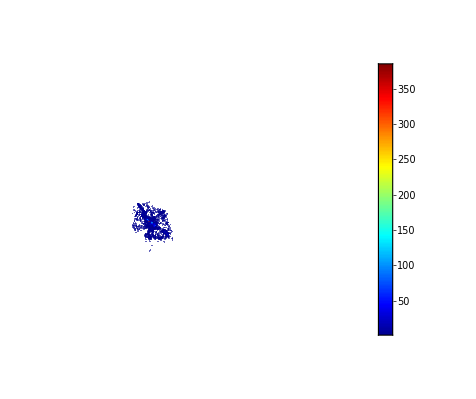

```mathematica
AllSourceLonLatHist
```

```mathematica
GeoArea[Polygon[GeoPosition[{{-77.25,50.336},{-77,53.935},{-77.25,53.935},{-77,57.534}}]]]
```

94.7272 mi^2

```mathematica
-86.25,-86,-140.411,-136.812,6}
{-86.25,-86,-136.812,-133.213,5}
```

```mathematica
GeoArea[Polygon[GeoPosition[{{-86.25,-140.411},{-86,-136.812},{-86.25,-136.812},{-86,-133.213}}]]]
```

8.91068 mi^2

```mathematica
AllSourceLonLatCluster
```

$Failed

```mathematica
GeoGraphics[GeoDisk[{-73,113},Quantity[50,"km"]]]
```